```mathematica
(* compute integral following substitution u=1/x *)
yMax = Integrate[1/(u^2+u^-4),{u,0,1}]
```

1/6 (π-√3 Log[2+√3])

```mathematica
Plot[yMax,{x,0,1}];
```

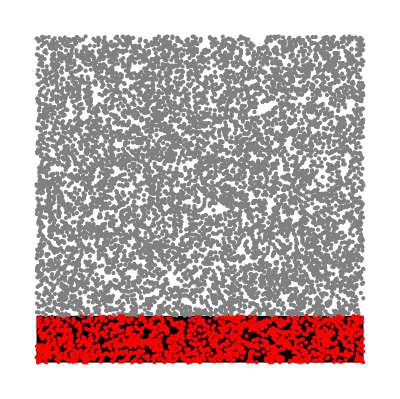

0.1394

```mathematica
(* sample n points uniformly in the (square [0,1])^2 *)
n = 100;

ℛ=Rectangle[{0,0},{1,yMax}];
boundingBox = Rectangle[{0,0},{1,1}];

data = RandomPoint[boundingBox,n];
col=RegionMember[ℛ,data]/. {False->Gray,True->Red};
Graphics[{ℛ,PointSize[Small],{col,Point/@data}ᵀ}]

(* calculate fraction of sampled points below function (within region ℛ) *)
N[Count[RegionMember[ℛ,data], True]/Length[data]]
```

```mathematica
(* plot E(N) *)
```